Jacobians and Eigen analysis

```mathematica
Clear["Global`*"]
```

Disease impacts ADULT stage

```mathematica
(* Equations *)
eqJ:=J'[t]==fS AS[t]+fI AI[t]-(m0-mb J[t]) J[t]-uJ J[t];(*Juvenile*)

eqAS:=AS'[t]==(m0-mb J[t]) J[t]-betaA AS[t] AI[t]-uA AS[t]; (*Susceptible Adult*)

eqAI:=AI'[t]==betaA AS[t] AI[t]-(uA+alphaA) AI[t]; (*Infected Adult*)

eqsol=FullSimplify[Solve[{eqJ[[2]]==0,eqAS[[2]]==0,eqAI[[2]]==0},{J[t],AS[t],AI[t]}]];
eqsol[[1]]
eqsol[[2]]
eqsol[[3]]
eqsol[[4]]
(* Jacobian 5 *)
Jac5 := ({{D[eqJ[[2]],J[t]], D[eqJ[[2]],AS[t]], D[eqJ[[2]],AI[t]]}, {D[eqAS[[2]],J[t]], D[eqAS[[2]],AS[t]], D[eqAS[[2]],AI[t]]}, {D[eqAI[[2]],J[t]], D[eqAI[[2]],AS[t]], D[eqAI[[2]],AI[t]]}})
MatrixForm[Jac5]
```

{J[t]→0,AS[t]→0,AI[t]→0}

{J[t]→(fS m0-uA (m0+uJ))/(mb (fS-uA)),AS[t]→(fS m0 uJ-uA uJ (m0+uJ))/(mb (fS-uA)^2),AI[t]→0}

{J[t]→(betaA m0 (alphaA-fI+uA)+betaA (alphaA+uA) uJ-√(betaA (-4 mb (alphaA+uA) (alphaA-fI+uA) (-fI uA+fS (alphaA+uA))+betaA (-fI m0+alphaA (m0+uJ)+uA (m0+uJ))^2)))/(2 betaA mb (alphaA-fI+uA)),AS[t]→(alphaA+uA)/betaA,AI[t]→(2 alphaA^2 mb (fS-uA)-2 fI fS mb uA+2 fI mb uA^2+2 fS mb uA^2-2 mb uA^3+2 alphaA mb (fI-2 uA) (-fS+uA)+betaA fI m0 uJ-betaA m0 uA uJ-betaA uA uJ^2-alphaA betaA uJ (m0+uJ)+uJ √(betaA (-4 mb (alphaA+uA) (alphaA-fI+uA) (-fI uA+fS (alphaA+uA))+betaA (-fI m0+alphaA (m0+uJ)+uA (m0+uJ))^2)))/(2 betaA mb (alphaA-fI+uA)^2)}

{J[t]→(betaA m0 (alphaA-fI+uA)+betaA (alphaA+uA) uJ+√(betaA (-4 mb (alphaA+uA) (alphaA-fI+uA) (-fI uA+fS (alphaA+uA))+betaA (-fI m0+alphaA (m0+uJ)+uA (m0+uJ))^2)))/(2 betaA mb (alphaA-fI+uA)),AS[t]→(alphaA+uA)/betaA,AI[t]→-((2 mb (alphaA+uA) (alphaA-fI+uA) (-fS+uA)+betaA uJ (m0 (alphaA-fI+uA)+(alphaA+uA) uJ)+uJ √(betaA (-4 mb (alphaA+uA) (alphaA-fI+uA) (-fI uA+fS (alphaA+uA))+betaA (-fI m0+alphaA (m0+uJ)+uA (m0+uJ))^2)))/(2 betaA mb (alphaA-fI+uA)^2))}

(-m0-uJ+2 mb J[t] | fS | fI
m0-2 mb J[t] | -uA-betaA AI[t] | -betaA AS[t]
0 | betaA AI[t] | -alphaA-uA+betaA AS[t])

Characteristic equation of Jacobian 5 evaluated for equilibrium in which J_I^* DOES NOT =0 (disease CAN persist).  Below lists polynomial coefficients starting with power 0.

```mathematica
FullSimplify[Eigenvalues[Jac5/.eqsol[[2]]]]
```

{-alphaA+(betaA m0 uJ)/(fS mb-mb uA)+uA (-1-(betaA uJ^2)/(mb (fS-uA)^2)),-1/(2 mb (fS-uA)^2)(√(mb^2 (fS-uA)^2 (-(fS-uA)^2 (4 fS m0-(m0+uA)^2)-2 (fS-uA) (fS (m0-3 uA)+uA (m0+uA)) uJ+(fS+uA)^2 uJ^2))+mb (fS-uA) (uA (m0-uA+uJ)+fS (-m0+uA+uJ))),1/(2 mb (fS-uA)^2)(√(mb^2 (fS-uA)^2 (-(fS-uA)^2 (4 fS m0-(m0+uA)^2)-2 (fS-uA) (fS (m0-3 uA)+uA (m0+uA)) uJ+(fS+uA)^2 uJ^2))-mb (fS-uA) (uA (m0-uA+uJ)+fS (-m0+uA+uJ)))}

```mathematica
FullSimplify[Eigenvalues[Jac5/.eqsol[[3]]]]
```

```mathematica
Coeff1 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac5/.eqsol[[1]],X],X]]
a0Eq1:=Coeff1[[1]]/Coeff1[[4]]
a1Eq1:=Coeff1[[2]]/Coeff1[[4]]
a2Eq1:=Coeff1[[3]]/Coeff1[[4]]
a3Eq1:=Coeff1[[4]]/Coeff1[[4]]

Coeff2 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac5/.eqsol[[2]],X],X]]
a0Eq2:=Coeff2[[1]]/Coeff2[[4]]
a1Eq2:=Coeff2[[2]]/Coeff2[[4]]
a2Eq2:=Coeff2[[3]]/Coeff2[[4]]
a3Eq2:=Coeff2[[4]]/Coeff2[[4]]

Coeff3 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac5/.eqsol[[3]],X],X]]
a0Eq3:=Coeff3[[1]]/Coeff3[[4]]
a1Eq3:=Coeff3[[2]]/Coeff3[[4]]
a2Eq3:=Coeff3[[3]]/Coeff3[[4]]
a3Eq3:=Coeff3[[4]]/Coeff3[[4]]

Coeff4 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac5/.eqsol[[4]],X],X]]
a0Eq4:=Coeff4[[1]]/Coeff4[[4]]
a1Eq4:=Coeff4[[2]]/Coeff4[[4]]
a2Eq4:=Coeff4[[3]]/Coeff4[[4]]
a3Eq4:=Coeff4[[4]]/Coeff4[[4]]

RHEq1:=a0Eq1>0&&a2Eq1>0&&a2Eq1*a1Eq1-a0Eq1>0
RHEq2:=a0Eq2>0&&a2Eq2>0&&a2Eq2*a1Eq2-a0Eq2>0
RHEq3:=a0Eq3>0&&a2Eq3>0&&a2Eq3*a1Eq3-a0Eq3>0
RHEq4:=a0Eq4>0&&a2Eq4>0&&a2Eq4*a1Eq4-a0Eq4>0
```

For stability, the three following Routh-Hurwitz criterion must be satisfied:
i) a0 > 0
ii) a2 > 0
iii) a2a1 - a0 > 0

Persistence

Extinction (* No feasible interior equilibrium *)
(* Neither eqsol[[2]], eqsol[[3]], eqsol[[4]] are feasible, interior (i.e., at least one of each eq is ≤ 0) *)
NoDisease (* No interior equilibrium, edge equilibrium exists *)
Stable (* Not Extinction case && all R-H criteria are fulfilled *)
Unstable (* Not Extinction case && at least one of the R-H criteria are violated *)

```mathematica
feasibleEq2:=eqsol[[2]][[1]][[2]]>0&&eqsol[[2]][[2]][[2]]> 0&&Im[eqsol[[2]][[1]][[2]]]==0(* &&Im[eqsol[[2]][[2]][[2]]]==0&&Im[eqsol[[2]][[3]][[2]]]==0 *)
feasibleEq3:=eqsol[[3]][[1]][[2]]>0&&eqsol[[3]][[2]][[2]]>0&&eqsol[[3]][[3]][[2]]>0;
feasibleEq4:=eqsol[[4]][[1]][[2]]>0&&eqsol[[4]][[2]][[2]]>0&&eqsol[[4]][[3]][[2]]>0;
InteriorExists:=feasibleEq3||feasibleEq4;
Extinction1:=!feasibleEq2&&!feasibleEq3&&!feasibleEq4; (* No feasible interior equilibrium *)
Extinction:=!feasibleEq3&&!feasibleEq4; (* No feasible interior equilibrium *)
(* Neither eqsol[[2]], eqsol[[3]], eqsol[[4]] are feasible, interior (i.e., at least one of each eq is ≤ 0) *)

ImEq2:=Im[eqsol[[2]][[1]][[2]]]==0&&Im[eqsol[[2]][[2]][[2]]]==0&&Im[eqsol[[2]][[3]][[2]]]==0
ImEq3:=Im[eqsol[[3]][[1]][[2]]]==0&&Im[eqsol[[3]][[2]][[2]]]==0&&Im[eqsol[[3]][[3]][[2]]]==0
ImEq4:=Im[eqsol[[4]][[1]][[2]]]==0&&Im[eqsol[[4]][[2]][[2]]]==0&&Im[eqsol[[4]][[3]][[2]]]==0


(* Im[Round[0.000000004,10^-10]] *)

NoDisease2:=!InteriorExists&&feasibleEq2
NoDisease:=feasibleEq2&&!feasibleEq3&&!feasibleEq4
StableEq2:=feasibleEq2&&RHEq2; 
StableEq3:=feasibleEq3&&RHEq3; 
StableEq4:=feasibleEq4&&RHEq4; 
UnstableEq3:=feasibleEq3&&!RHEq3
UnstableEq4:=feasibleEq4&&!RHEq4
Stable := StableEq3||StableEq4; (* Interior exists and Dom Eig is stable *)
Unstable:=UnstableEq3||UnstableEq4;(* Interior exists and Dom Eig is not stable *)
DoubleCheck1:=UnstableEq3&&UnstableEq4
DoubleCheck2:=StableEq3&&StableEq4
```

Figure 2D

Greater::nord: Invalid comparison with 7.5004-377.278 ⅈ attempted.

Greater::nord: Invalid comparison with 47460.+377.398 ⅈ attempted.

Greater::nord: Invalid comparison with -1.4998+188.609 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

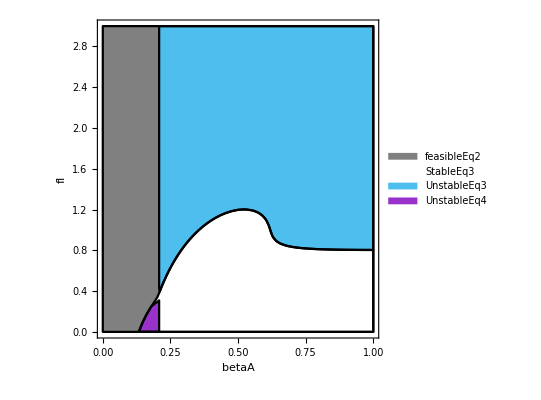

Figure 2E

Greater::nord: Invalid comparison with 7.50033-413.292 ⅈ attempted.

Greater::nord: Invalid comparison with 47458.8+344.501 ⅈ attempted.

Greater::nord: Invalid comparison with -1.7998+247.943 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

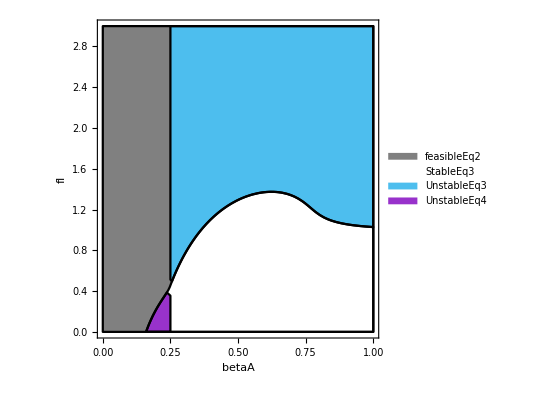

Figure 2F

Greater::nord: Invalid comparison with 7.5002-533.57 ⅈ attempted.

Greater::nord: Invalid comparison with 47456.3+266.827 ⅈ attempted.

Greater::nord: Invalid comparison with -2.9998+533.527 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

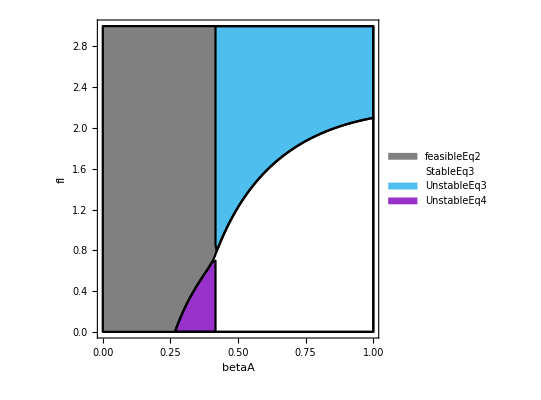

```mathematica
fS=3;
uJ=0.5;
m0=2.5;
alphaA=0; (*0.1;*)
uA=0.5;
mb=0.2;

"Figure 2D"
RegionPlot[{feasibleEq2,StableEq3,UnstableEq3, StableEq4, UnstableEq4},{betaA,0,1.0}, {fI,0 , fS}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large, RotateLabel-> False,PlotStyle->{RGBColor[0.5, 0.5, 0.5], White, RGBColor[0.301, 0.745, 0.933], White,RGBColor[153/256,50/256,204/256]},BoundaryStyle->{Black}]

"Figure 2E"
alphaA=0.1;
RegionPlot[{feasibleEq2,StableEq3,UnstableEq3, StableEq4, UnstableEq4},{betaA,0,1.0}, {fI,0 , fS}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large, RotateLabel-> False,PlotStyle->{RGBColor[0.5, 0.5, 0.5], White, RGBColor[0.301, 0.745, 0.933], White,RGBColor[153/256,50/256,204/256]},BoundaryStyle->{Black}]

"Figure 2F"
alphaA=0.5;
RegionPlot[{feasibleEq2,StableEq3,UnstableEq3, StableEq4, UnstableEq4},{betaA,0,1.0}, {fI,0 , fS}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large, RotateLabel-> False,PlotStyle->{RGBColor[0.5, 0.5, 0.5], White, RGBColor[0.301, 0.745, 0.933], White,RGBColor[153/256,50/256,204/256]},BoundaryStyle->{Black}]
```